```mathematica
ClearAll["Global`*"];
result=Import[FileNameJoin[{NotebookDirectory[],"dft.dat"}]];
input=Import[FileNameJoin[{NotebookDirectory[],"original.dat"}]];
```

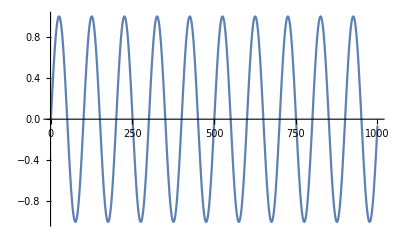

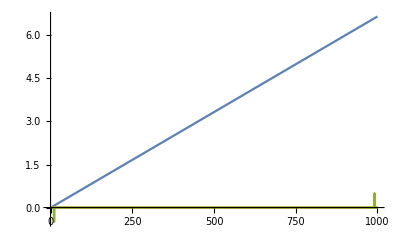

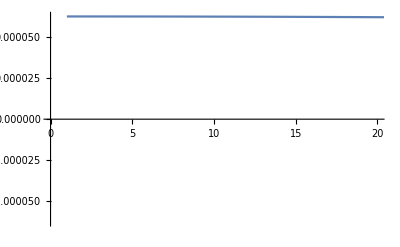

```mathematica
ListPlot[Transpose[input],Joined->True]
ListPlot[Transpose[result],Joined->True,PlotRange->All]
ListPlot[Transpose[result][[2]],Joined->True,PlotRange->{{0,20},All}]
```

Power::infy: 無限式1/0が見付かりました．

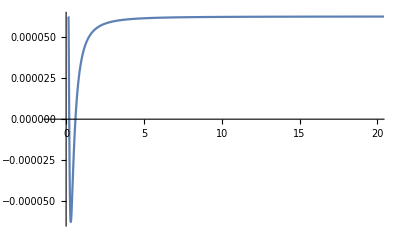

```mathematica
T0=15;
data=Transpose[result];
ListPlot[Transpose@{1/data[[1]],data[[2]]},Joined->True,PlotRange->{{-1,20},All}]
```